# Finding a Parametrization for the Rough Diffuse Surface Simulation

We wrote a program that is capable of generating or loading a microsurface and ray-tracing that surface using a very large amount of rays (several hundred millions), thus obtaining the distribution of outgoing directions after 1 or more scattering events (up to 4).
We gathered the outgoing lobes for different parameters of the surface:
	• Angle of incidence
	• Roughness
	• Albedo

We then performed a fitting of the simulated data using a modified cosine lobel model that uses non-uniform scaling and a local tangent space.
The matrix M allows to transform from local lobe space to surface space:

	A=(T
B
σ_n R(θ_l))
	ω_w= (ω_l ·A)/(|ω_l ·A|)
	ω_l= (ω_w· A^-1)/(|ω_w ·A^-1|)
	
ω_l is the local lobe-space unit vector
ω_w is the surface-space unit vector after renormalization
R(θ_l) is the lobe’s principal axis (usually, the reflected incoming direction). It’s defined by one of the parameters of the lobe model θ_l
T, B are the complementary vectors forming an orthonormal basis with N
σ_n is a non-uniform scaling factor along the lobe’s principal direction and another one of the parameters of the lobe model

#### Lobe Intensity in Local-Space, Given Two Directions in Surface-Space

Once in local lobe-space, the intensity of the lobe is given by:

	f(ω_o,ω_i,ρ,σ,μ) = σ [(1-μ) + μ G(ω_o·Z,ρ) G(ω_i·Z,ρ)] N( ω_i, ρ )
	
	G(θ,ρ) = Piecewise[{{(3.535 a + 2.181 a^2)/(1.0 + 2.276 a + 2.577 a^2), a(θ,ρ) < 1.6}, {1, otherwise}}]
	a(θ,ρ) = (√(1+(α(ρ))/2))/(tan(θ))
	N( ω_i, ρ ) =  (2+α(ρ))/π [(ω_i ·A^-1)/(|ω_i ·A^-1|).Z]^(α(ρ))	
	α(ρ)= 2^(10(1-ρ))-1
	
	ω_o is the outgoing view direction in surface space
	ω_i is the incoming light direction in surface space
	σ is the global scale factor
	μ is the masking importance factor in [0,1] that allows to bypass the masking term (μ=0) completely.
	G(θ,ρ) is the masking term for the Phong model
	N( ω_i, ρ ) defines the cosine lobe’s intensity using roughness, angle from local normal axis and global scale
	α(ρ) defines the exponent based on the surface’s roughness (notice the -1 in the end that allows use to have a 0 exponent to make constant lobes)
	Z is the unit Z-up vector (0,0,1)

```mathematica
Lobe Intensity in Surface-Space
```

- +in Intensity Lobe Surface

We need to quickly find the length of the surface-space vector ω_w when transformed from local lobe-space to suface-space:

	L = |ω_l·A|

We know that for an unscaled lobe direction ω_l we get the scaled version ω_s:

	ω_s = ω_l (1 | 0 | 0
0 | 1 | 0
0 | 0 | σ_n)
	L = |ω_s|
	
And the unit surface-space direction is:

	ω_w= ω_s/L

Now, if we write:

	ω_l =ω_w (L | 0 | 0
0 | L | 0
0 | 0 | L/σ_n)

Since |ω_l| = 1 :

	|ω_w (L | 0 | 0
0 | L | 0
0 | 0 | L/σ_n)|=1

This lets us solve for L:

	L(σ_n) = 1/(√(1+[ω_w · Z]^2 (1/σ_n^2-1)))

So in the end, we can estimate the final lobe size in surface-space as:

	f_w(ω_o,ω_i,ρ,σ,σ_n,μ) = L(σ_n) f(ω_o,ω_i,ρ,σ,μ)


Building the Local Tangent Space

Knowing the incoming light direction ω_i (pointing away from the surface) and assuming it’s pointing upward, we can easily setup T_0 as:

	T_0 = ((0,1,0) × ω_i)/(|(0,1,0) × ω_i|)
	
This gives us a flat base to orient our cosine lobe:

	R(θ) = cos(θ) (0,0,1) sin(θ) T_0

From R(θ) it’s easy to retrieve T and B as:

	T = (R(θ) × (0,0,1))/(|R(θ) × (0,0,1)|)
	B = T × R(θ)

# Parametrization

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness ρ
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance μ

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]] (* So Mathematica knows the directory for our files *)
str=OpenRead["results_order2_slice0.bin",{BinaryFormat->True}]
rawFile0= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\1) Analytical Flattening\Export

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice1.bin",{BinaryFormat->True}]
rawFile1= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice2.bin",{BinaryFormat->True}]
rawFile2= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice3.bin",{BinaryFormat->True}]
rawFile3= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
(* Organize raw list into a proper 2D array depending on suface's theta/roughness *)
resX=20;
resY=10;
table0=Table[rawFile0[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table1=Table[rawFile1[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table2=Table[rawFile2[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table3=Table[rawFile3[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
MatrixForm[table0];
```

```mathematica
table0[[10,20]]
```

{0.,1.,1.×10^-6,0.21592,0.}

Parametrizing Theta

```mathematica
paramsTheta0 = Table[table0[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta1 = Table[table1[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta2 = Table[table2[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta3 = Table[table3[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsTheta0]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Show[ListPlot3D[paramsTheta0,{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta1,{ColorFunction->RGBColor[0,1,0],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta2,{ColorFunction->RGBColor[0,0,1],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta3,{ColorFunction->RGBColor[1,1,0],PlotRange->{0,π/2}}] ]
```

-Graphics3D-

No surprise there : the diffuse lobe is almost static and has no prefered direction so θ = 0 ⟹ One less parameter to worry about!
NOTE: Now it’s completely flat because I really constrained the θ parameter to 0 in subsequent simulations.

Fitting Lobe Roughness

```mathematica
paramsRho0 = Table[table0[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsRho1 = Table[table1[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsRho2 = Table[table2[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsRho3 = Table[table3[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsRho0]
```

(0.894891 | 0.895525 | 0.893949 | 0.893651 | 0.893649 | 0.893648 | 0.893678 | 0.89376 | 0.893951 | 0.894129 | 0.894574 | 0.895243 | 0.901814 | 0.897432 | 0.899196 | 0.901601 | 0.904829 | 0.909352 | 0.916303 | 0.925811
0.894733 | 0.894731 | 0.901542 | 0.895808 | 0.894568 | 0.894538 | 0.894595 | 0.89463 | 0.894775 | 0.894893 | 0.895186 | 0.895582 | 0.896224 | 0.897225 | 0.898582 | 0.900452 | 0.903382 | 0.909011 | 0.913457 | 0.930018
0.901717 | 0.897237 | 0.896142 | 0.903866 | 0.895864 | 0.895865 | 0.897254 | 0.895912 | 0.895972 | 0.896035 | 0.90634 | 0.896444 | 0.897273 | 0.898693 | 0.898706 | 0.900383 | 0.902449 | 0.906033 | 0.911028 | 0.920467
0.90958 | 0.906259 | 0.897778 | 0.907885 | 0.898805 | 0.900489 | 0.897772 | 0.906356 | 0.898546 | 0.897932 | 0.906741 | 0.898177 | 0.899124 | 0.9099 | 0.899811 | 0.90279 | 0.902882 | 0.905171 | 0.909969 | 0.92551
0.900722 | 0.905765 | 0.915368 | 0.913918 | 0.900522 | 0.906647 | 0.908698 | 0.91242 | 0.904719 | 0.900523 | 0.908555 | 0.900952 | 0.908718 | 0.901589 | 0.901446 | 0.906825 | 0.903677 | 0.905891 | 0.90957 | 0.926877
0.904136 | 0.9099 | 0.904049 | 0.904033 | 0.905493 | 0.905447 | 0.903984 | 0.920446 | 0.904183 | 0.904067 | 0.905378 | 0.907723 | 0.90646 | 0.905322 | 0.9072 | 0.904976 | 0.905733 | 0.907149 | 0.910865 | 0.930544
0.908814 | 0.908712 | 0.908689 | 0.908828 | 0.908681 | 0.90879 | 0.908876 | 0.908731 | 0.90868 | 0.909048 | 0.909001 | 0.909064 | 0.908735 | 0.908802 | 0.908893 | 0.909094 | 0.909496 | 0.910809 | 0.914541 | 0.931686
0.918765 | 0.920731 | 0.920362 | 0.920224 | 0.924523 | 0.920581 | 0.919947 | 0.91949 | 0.91983 | 0.920099 | 0.919382 | 0.919931 | 0.920653 | 0.920195 | 0.91934 | 0.923237 | 0.923127 | 0.921765 | 0.926501 | 0.931162
0.928363 | 0.928294 | 0.928227 | 0.92839 | 0.928388 | 0.928374 | 0.928447 | 0.928352 | 0.928353 | 0.928254 | 0.92838 | 0.928252 | 0.928307 | 0.928401 | 0.928309 | 0.928332 | 0.928432 | 0.928594 | 0.929073 | 0.950207
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
rho2exponent[ρ_] := 2^(10*(1-ρ))-1
rho2exponent[0.95913]
```

0.327489

```mathematica
ListPlot3D[rho2exponent[paramsRho0],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[rho2exponent[paramsRho1],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[rho2exponent[paramsRho2],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[rho2exponent[paramsRho3],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

It would seem that, ignoring the last 2 or 3 rows of each array, we have quite a uniform roughness.
Averaging roughnesses we obtain:

```mathematica
avgRho0 = Sum[paramsRho0[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgRho1 = Sum[paramsRho1[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgRho2 = Sum[paramsRho2[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgRho3 = Sum[paramsRho3[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
```

0.904175

0.908447

0.949484

0.996362

```mathematica
avgExponent0=rho2exponent[avgRho0]
avgExponent1=rho2exponent[avgRho1]
avgExponent2=rho2exponent[avgRho2]
avgExponent3=rho2exponent[avgRho3]
```

0.942948

0.886266

0.419279

0.0255391

So we could use an average exponent of 0.7, maybe 0.5 so we could simply take the square root of the cosine term?

Matching Lobe Global Scale

```mathematica
paramsScale0 = Table[table0[[j]][[i]][[3]],{j,1,resY},{i,1,resX}]
paramsScale1 = Table[table1[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale2 = Table[table2[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale3 = Table[table3[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
```

{{0.560032,0.559434,0.571278,0.58573,0.594506,0.597278,0.599239,0.601832,0.603896,0.604937,0.605022,0.604944,0.621166,0.602683,0.599918,0.594014,0.584266,0.569417,0.546772,0.508242},{0.580672,0.577256,0.584544,0.604565,0.613474,0.615438,0.616654,0.618711,0.62106,0.621965,0.621504,0.622244,0.621576,0.621082,0.619461,0.61491,0.60669,0.612407,0.588251,0.963255},{0.600409,0.593033,0.605849,0.612661,0.628033,0.629068,0.628256,0.631468,0.633243,0.633884,0.628677,0.633826,0.634075,0.632075,0.632784,0.6316,0.62385,0.61267,0.593264,0.535137},{0.625075,0.596258,0.613637,0.623155,0.633332,0.630363,0.632921,0.631174,0.635565,0.635849,0.63259,0.635422,0.63585,0.679695,0.635499,0.632488,0.629309,0.617972,0.598029,0.517066},{0.609013,0.59755,0.600784,0.613855,0.624894,0.618145,0.615624,0.608576,0.619533,0.623727,0.615256,0.622571,0.617848,0.623097,0.623215,0.620916,0.620546,0.612805,0.593475,0.487834},{0.582012,0.567215,0.574574,0.58384,0.588124,0.584713,0.584545,0.601197,0.586381,0.587028,0.58744,0.585071,0.584209,0.585505,0.586538,0.586851,0.586084,0.581049,0.56458,0.429902},{0.517867,0.505384,0.508125,0.514492,0.518457,0.514483,0.51313,0.514192,0.515311,0.515808,0.516099,0.515412,0.514519,0.514498,0.514824,0.515213,0.514803,0.511592,0.500968,0.341453},{0.392097,0.385718,0.386268,0.388464,0.389067,0.387963,0.387433,0.388126,0.388485,0.388527,0.388747,0.388364,0.387917,0.387902,0.387921,0.387442,0.387108,0.385378,0.377855,0.215805},{0.218231,0.218178,0.218228,0.218257,0.218233,0.218129,0.21796,0.217919,0.217823,0.217769,0.217672,0.217637,0.21752,0.217452,0.217395,0.217258,0.217054,0.216547,0.214901,0.0871064},{1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6}}

```mathematica
ListPlot3D[paramsScale0,{ PlotRange->{0,0.7},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale1,{ PlotRange->{0,0.4},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsScale2,{ PlotRange->{0,0.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsScale3,{ PlotRange->{0,0.05},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

### Representative Shape

All surfaces seem to behave in approximately the same way: a curved slope → 0 when roughness → 0 (which is quite logical since a smooth surface won’t show additional scattering orders).
The base height of the curved surface is then dependent on albedo in a way we will see in a second time.

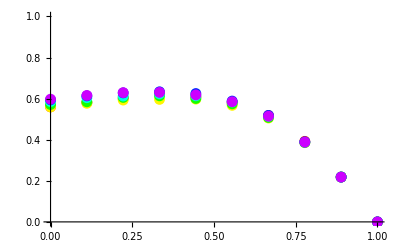

```mathematica
valuesS=Table[Table[{(j-1)/(resY-1),paramsScale0[[j]][[i]]},{j,1,resY}],{i,1,19}];
Show[Table[ListPlot[valuesS[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

### Choosing the Model

(a→0.557711 | b→0.202753 | c→0.297891 | d→-1.0633
a→0.560117 | b→0.0936903 | c→0.480266 | d→-1.13739
a→0.569968 | b→0.124168 | c→0.378029 | d→-1.07544
a→0.585732 | b→0.111557 | c→0.376861 | d→-1.07859
a→0.593691 | b→0.157631 | c→0.245544 | d→-1.00112
a→0.597623 | b→0.128056 | c→0.275238 | d→-1.00417
a→0.599521 | b→0.120897 | c→0.277818 | d→-1.00132
a→0.602605 | b→0.0969916 | c→0.348538 | d→-1.05269
a→0.604177 | b→0.12139 | c→0.266114 | d→-0.99495
a→0.604809 | b→0.12677 | c→0.256022 | d→-0.991176)

(0.557711+0.202753 u+0.297891 u^2-1.0633 u^3
0.560117+0.0936903 u+0.480266 u^2-1.13739 u^3
0.569968+0.124168 u+0.378029 u^2-1.07544 u^3
0.585732+0.111557 u+0.376861 u^2-1.07859 u^3
0.593691+0.157631 u+0.245544 u^2-1.00112 u^3
0.597623+0.128056 u+0.275238 u^2-1.00417 u^3
0.599521+0.120897 u+0.277818 u^2-1.00132 u^3
0.602605+0.0969916 u+0.348538 u^2-1.05269 u^3
0.604177+0.12139 u+0.266114 u^2-0.99495 u^3
0.604809+0.12677 u+0.256022 u^2-0.991176 u^3)

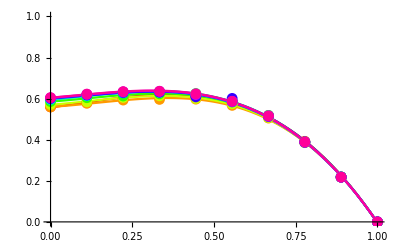

```mathematica
Clear[a,b,c,d]
modelS=a+b*u+c*u^2;
modelS=a+b*u+c*u^2+d*u^3;
fittingS = Table[FindFit[ valuesS[[j]],modelS,{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingS]
MatrixForm[modelS/.fittingS]
Show[Table[Plot[modelS/.fittingS[[j]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(j-1)/resY]],{j,1,resY}],
Table[ListPlot[valuesS[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.1*(i-1)]],{i,1,resY}]]
```

### Averaging a Unique Fit

{a→0.587595,b→0.128391,c→0.320232,d→-1.04001}

0.587595+0.128391 (1-ρ)+0.320232 (1-ρ)^2-1.04001 (1-ρ)^3

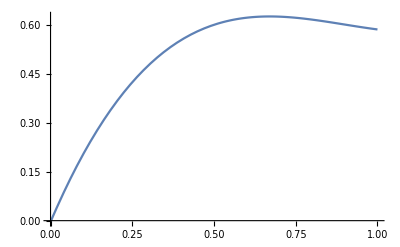

```mathematica
Clear[parmsS,fS,u,ρ]
parmsS={a->1/resY Sum[a/.fittingS[[j]],{j,1,resY}],b-> 1/resY Sum[b/.fittingS[[j]],{j,1,resY}],c-> 1/resY Sum[c/.fittingS[[j]],{j,1,resY}],d-> 1/resY Sum[d/.fittingS[[j]],{j,1,resY}]}
fS[ρ_]=Evaluate[modelS/.parmsS/.u->1-ρ]
(*fS[ρ_]=Function[{u},Evaluate[modelS/.parmsS]]*)
Plot[fS[ρ],{ρ,0,1}]
```

### Finding Dependence on Albedo

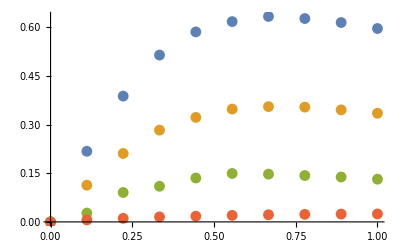

```mathematica
avgParamsScale= { 
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale0[[j]][[i]],{i,3,18}]},{j,1,resY}],
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale1[[j]][[i]],{i,3,18}]},{j,1,resY}],
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale2[[j]][[i]],{i,3,18}]},{j,1,resY}],
Table[{1-(j-1)/(resY-1),1/16 Sum[paramsScale3[[j]][[i]],{i,3,18}]},{j,1,resY}] };
MatrixForm[avgParamsScale];
ListPlot[avgParamsScale]
```

(amp→1.00898
amp→0.562955
amp→0.228768
amp→0.0349632)

(1.00898 (0.587595+0.128391 (1-u)+0.320232 (1-u)^2-1.04001 (1-u)^3)
0.562955 (0.587595+0.128391 (1-u)+0.320232 (1-u)^2-1.04001 (1-u)^3)
0.228768 (0.587595+0.128391 (1-u)+0.320232 (1-u)^2-1.04001 (1-u)^3)
0.0349632 (0.587595+0.128391 (1-u)+0.320232 (1-u)^2-1.04001 (1-u)^3))

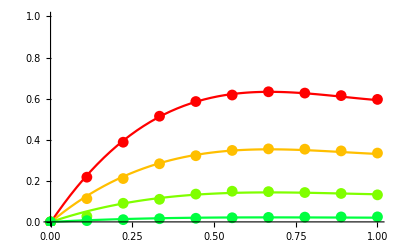

```mathematica
Clear[modelS2]
pipo = Function[{u},Evaluate[modelS/.parmsS]];
modelS2=amp*fS[u];
fittingS2 = Table[FindFit[ avgParamsScale[[albedo]],modelS2,{amp},u ],{albedo,1,4}];
MatrixForm[fittingS2]
MatrixForm[modelS2/.fittingS2]
Show[Table[Plot[modelS2/.fittingS2[[albedo]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(albedo-1)/8]],{albedo,1,4}],
Table[ListPlot[avgParamsScale[[albedo]],PlotRange->{0,1} , PlotStyle->Hue[(albedo-1)/8]],{albedo,1,4}]]
```

Intuitively, and it’s pretty much verified, although more albedo simulations should be performed, it seems the amplitude of the scale parameter is dependent on albedo^2.
It is expected that the amplitude for scattering order 3 will be dependent on albedo^3 and so on... (To be verified!)

### Simulating More Albedos

Just to be on the safe side, as it’s an extremely important parameter, we will create a new document that will simulate fewer elements in θ and ρ but a lot more samples in albedo:

Matching Lobe Flattening Factor ==> FIRST PARAMETER MATCHED!

```mathematica
paramsFlat0 = Table[table0[[j]][[i]][[4]],{j,1,resY},{i,1,resX}]
paramsFlat1 = Table[table1[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat2 = Table[table2[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat3 = Table[table3[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
```

{{0.698427,0.698444,0.698497,0.698591,0.698737,0.698951,0.699257,0.699696,0.700327,0.701241,0.702581,0.704572,0.707565,0.712118,0.719115,0.729968,0.74692,0.773535,0.815435,0.881422},{0.644619,0.644627,0.644653,0.644699,0.644771,0.644878,0.645036,0.645268,0.64561,0.646125,0.646908,0.648121,0.650025,0.65306,0.657961,0.665964,0.679151,0.701023,0.737445,0.798169},{0.591127,0.591131,0.591143,0.591165,0.5912,0.591252,0.591331,0.591449,0.59163,0.591911,0.592356,0.593073,0.594249,0.596214,0.599547,0.605278,0.615238,0.632692,0.663436,0.7177},{0.537773,0.537775,0.53778,0.53779,0.537806,0.537831,0.537869,0.537928,0.53802,0.538169,0.538413,0.538823,0.539527,0.540759,0.542954,0.546928,0.554214,0.567703,0.592836,0.639798},{0.484477,0.484478,0.484481,0.484485,0.484492,0.484503,0.484521,0.484549,0.484595,0.48467,0.4848,0.485025,0.485431,0.486174,0.487565,0.490217,0.495346,0.505377,0.525148,0.564259},{0.431207,0.431207,0.431208,0.43121,0.431213,0.431218,0.431226,0.431239,0.43126,0.431297,0.431361,0.43148,0.431701,0.432127,0.432965,0.434646,0.438077,0.445166,0.459945,0.490897},{0.377947,0.377947,0.377948,0.377948,0.37795,0.377951,0.377955,0.37796,0.377969,0.377986,0.378016,0.378073,0.378185,0.378411,0.378878,0.379865,0.38199,0.386629,0.396858,0.419538},{0.324691,0.324691,0.324692,0.324692,0.324692,0.324693,0.324694,0.324696,0.324699,0.324706,0.324718,0.324742,0.324792,0.324896,0.325122,0.325626,0.32677,0.32941,0.335567,0.350019},{0.271437,0.271437,0.271437,0.271437,0.271438,0.271438,0.271438,0.271439,0.271439,0.271441,0.271445,0.271452,0.271467,0.2715,0.271576,0.271755,0.272183,0.273226,0.275799,0.282193},{0.218184,0.218184,0.218184,0.218184,0.218184,0.218184,0.218184,0.218184,0.218184,0.218184,0.218183,0.218182,0.21818,0.218174,0.218162,0.218131,0.218052,0.217848,0.217317,0.21592}}

```mathematica
ListPlot3D[paramsFlat0,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsFlat1,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsFlat2,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsFlat3,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

### Representative Shape

We see that for albedo 1 and 0.75, the shape is pretty similar and that for lower albedos the change was neglected and is always 1.
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in ρ is from index 1 to about 6.

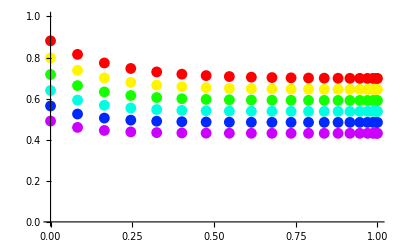

```mathematica
test=Table[{(i-1)/(resX-1),  paramsFlat0[[1]][[i]]},{i,1,resX}];
ListPlot[test];
valuesSn=Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,6}];
Show[Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

### Choosing the Model

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

(a→51.7133 | b→-50.9138 | c→-0.00234346
a→41.1142 | b→-40.39 | c→-0.00234953
a→36.0176 | b→-35.3646 | c→-0.00210165
a→0.537742 | b→0.102009 | c→7.43738
a→22.7258 | b→-22.2061 | c→-0.00192833
a→17.7564 | b→-17.3 | c→-0.00177817)

(51.7133-50.9138 ⅇ^(0.00234346 u)
41.1142-40.39 ⅇ^(0.00234953 u)
36.0176-35.3646 ⅇ^(0.00210165 u)
0.537742+0.102009 ⅇ^(-7.43738 u)
22.7258-22.2061 ⅇ^(0.00192833 u)
17.7564-17.3 ⅇ^(0.00177817 u))

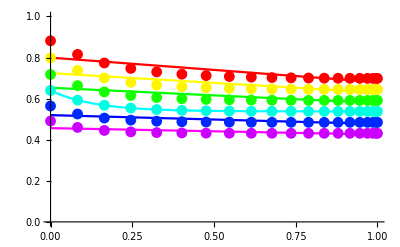

```mathematica
Clear[a,b,c]
modelSn=a+b*Exp[-c * u];
fittingSn = Table[FindFit[ valuesSn[[j]],modelSn,{a,b,c},u ],{j,1,6}];
MatrixForm[fittingSn]
MatrixForm[modelSn/.fittingSn]
Show[Table[Plot[modelSn/.fittingSn[[j]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(j-1)/6]],{j,1,6}],
Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

#### Matching Parameters

Now that we have a bunch of nice expressions for representing f(cos(θ)), we need to find tendencies in the fitted parameters a, b and c.

46.913-66.9676 x

-46.1135+66.3653 x

0.70613+1.91406 x

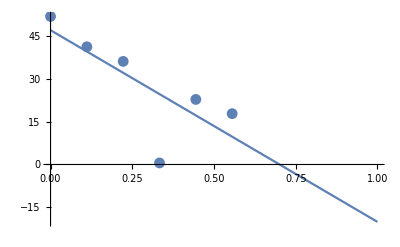

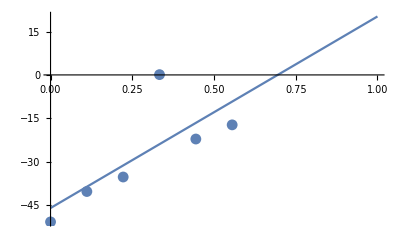

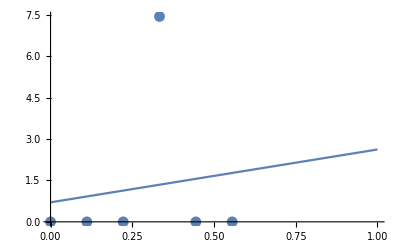

```mathematica
fa = Table[{(j-1)/9,a/.fittingSn[[j]]}, {j,1,6}];
fb = Table[{(j-1)/9,b/.fittingSn[[j]]}, {j,1,6}];
fc= Table[{(j-1)/9,c/.fittingSn[[j]]}, {j,1,6}];
mfa = LinearModelFit[fa,x,x];
mfb = LinearModelFit[fb,x,x];
mfc = LinearModelFit[fc,x,x];
Normal[mfa]
Normal[mfb]
Normal[mfc]
Show[ListPlot[fa,PlotRange->{0,1}],Plot[mfa[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fb,PlotRange->{0,1}],Plot[mfb[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fc,PlotRange->{0,10}],Plot[mfc[x],{x,0,1}],PlotRange->All]
```

#### Final Expression

We can now obtain the final expression for the function matching the lobe flattening factor:

a(ρ) = 0.697462 - 0.479278 (1-ρ)
b(ρ) = 0.287646 - 0.293594 (1-ρ)
c(ρ) = 5.69744 + 6.61321 (1-ρ)
μ = cos(θ)
f( μ, ρ ) = a(ρ) + b(ρ) e^(-c(ρ)  μ)

```mathematica
a[ρ_] = 0.697462 - 0.479278 (1-ρ);
b[ρ_] = 0.287646 - 0.293594 (1-ρ);
c[ρ_] = 5.69744 + 6.61321 (1-ρ);
f[ μ_, ρ_] = a[ρ] + b[ρ] Exp[-c[ρ]  μ];

Plot3D[f[μ,ρ],{μ,0,1},{ρ,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","ρ","Lobe Flattening"}]
```

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","ρ"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

Matching Masking Importance

```mathematica
paramsMask0 = Table[table0[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask1 = Table[table1[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask2 = Table[table2[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask3 = Table[table3[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
```

```mathematica
ListPlot3D[paramsMask0,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask1,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask2,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsMask3,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

-Graphics3D-